```mathematica
cn=0.645;
ct=0.635779246332329;
(*cn=0;
ct=0;*)
(*Remove[cn]
cn=0;*)

infplaneN[z_,a_]=1-9/(8(z/a+cn))+1/(2(z/a+cn)^3)-1/(8(z/a+cn)^5);
infplaneT[z_,a_]=1-9/(16(z/a+ct))+2/(16(z/a+ct)^3)-1/(16(z/a+ct)^5);

MCSAN[z_,a_,LL_]=(1+Sum[(-1)^n(1/(infplaneN[z,a](n LL/a +(z/a)))-1),{n,0,5}]+Sum[(-1)^n(1/(infplaneN[z,a]((n+1) LL/a -(z/a)))-1),{n,0,5}])^-1
```

1/(1+a/(z (1-1/(8 (0.645+z/a)^5)+1/(2 (0.645+z/a)^3)-9/(8 (0.645+z/a))))+1/((LL/a-z/a) (1-1/(8 (0.645+z/a)^5)+1/(2 (0.645+z/a)^3)-9/(8 (0.645+z/a))))-1/(((2 LL)/a-z/a) (1-1/(8 (0.645+z/a)^5)+1/(2 (0.645+z/a)^3)-9/(8 (0.645+z/a))))+1/(((3 LL)/a-z/a) (1-1/(8 (0.645+z/a)^5)+1/(2 (0.645+z/a)^3)-9/(8 (0.645+z/a))))-1/(((4 LL)/a-z/a) (1-1/(8 (0.645+z/a)^5)+1/(2 (0.645+z/a)^3)-9/(8 (0.645+z/a))))+1/(((5 LL)/a-z/a) (1-1/(8 (0.645+z/a)^5)+1/(2 (0.645+z/a)^3)-9/(8 (0.645+z/a))))-1/(((6 LL)/a-z/a) (1-1/(8 (0.645+z/a)^5)+1/(2 (0.645+z/a)^3)-9/(8 (0.645+z/a))))-1/((LL/a+z/a) (1-1/(8 (0.645+z/a)^5)+1/(2 (0.645+z/a)^3)-9/(8 (0.645+z/a))))+1/(((2 LL)/a+z/a) (1-1/(8 (0.645+z/a)^5)+1/(2 (0.645+z/a)^3)-9/(8 (0.645+z/a))))-1/(((3 LL)/a+z/a) (1-1/(8 (0.645+z/a)^5)+1/(2 (0.645+z/a)^3)-9/(8 (0.645+z/a))))+1/(((4 LL)/a+z/a) (1-1/(8 (0.645+z/a)^5)+1/(2 (0.645+z/a)^3)-9/(8 (0.645+z/a))))-1/(((5 LL)/a+z/a) (1-1/(8 (0.645+z/a)^5)+1/(2 (0.645+z/a)^3)-9/(8 (0.645+z/a)))))

```mathematica
MCSAN[5a0,a0,width ]
width/a0
```

0.797068

50.9961

{{25.498,0.951},{12.749,0.9188},{6.37451,0.8337},{3.18726,0.6729},{1.59363,0.4248},{0.796814,0.1949},{0.398407,0.06222},{0.,0},{0.,0},{0.,0},{0.,0},{0.,0}}

{{22.5134,0.9596},{11.2567,0.9246},{5.62835,0.8306},{2.81417,0.6533},{1.40709,0.3928},{0.703543,0.1643},{0.351772,0.051},{0.,0},{0.,0},{0.,0},{0.,0},{0.,0}}

0.989214+152.697/(2.62177+x)^5-33.2256/(2.62177+x)^3-0.991641/(2.62177+x)

0.997086+156.99/(2.60254+x)^5-34.903/(2.60254+x)^3-0.863661/(2.60254+x)

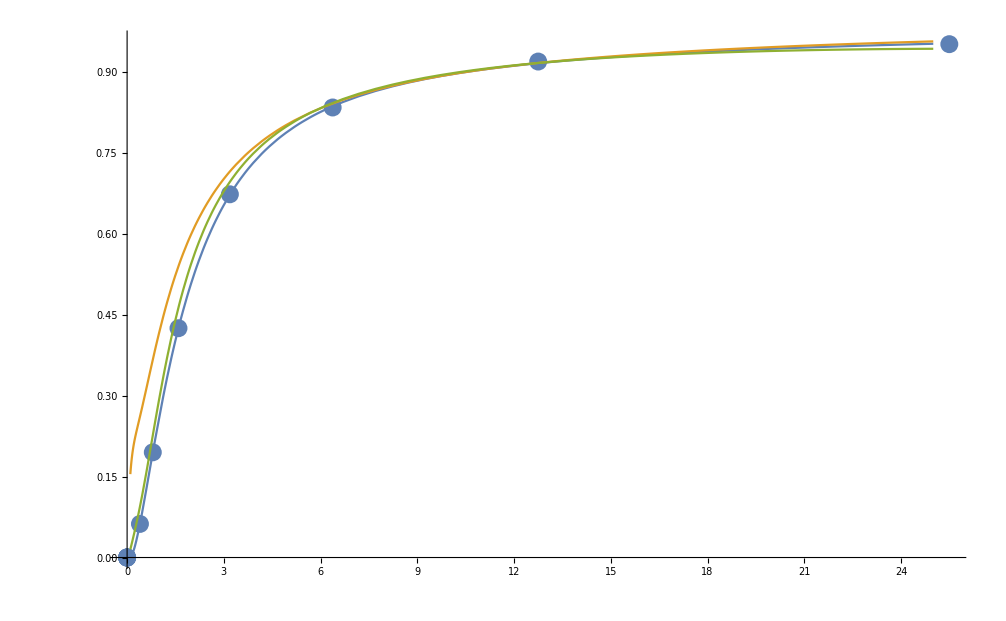

```mathematica
(*normal, measured at 256*64*256*)
width=8.284925963482451*10^-7;
L={1/2,1/4,1/8,1/16,1/32,1/64,1/128,0,0,0,0,0}*width;
a0=1.62462*10^-8;
mobwet0={0.9510,0.9188,0.8337,0.6729,0.4248,0.1949,0.06222,0,0,0,0,0};
ratio0=L/a0;
curve0=Thread[{ratio0,mobwet0}]

a1=1.84*10^-8;
mobwet1={0.9596,0.9246,0.8306,0.6533,0.3928,0.1643,0.05100,0,0,0,0,0};
ratio1=L/a1;
curve1=Thread[{ratio1,mobwet1}]

fitfunc2=aa+bb 1/(x+ctf)+cc 1/(x+ctf)^3+dd 1/(x+ctf)^5;
fit0[x_]=fitfunc2/. FindFit[ curve0,fitfunc2,{aa,bb,cc,dd,ee,ctf},x]
fit1[x_]=fitfunc2/. FindFit[ curve1,fitfunc2,{aa,bb,cc,dd,ee,ctf},x]

p1=ListPlot[{curve0},PlotRange->All];
p2=Plot[{fit0[x],infplaneN[x a0,a0],MCSAN[x a0,a0,width]},{x,0.1,25},PlotRange->All];
Show[p1,p2,PlotRange->All]
```

```mathematica
D[fit0[z/a],z]
```

-763.486/(a (2.62177+z/a)^6)+99.6767/(a (2.62177+z/a)^4)+0.991641/(a (2.62177+z/a)^2)

{{25.498,0.9618},{12.749,0.9491},{6.37451,0.9093},{3.18726,0.8256},{1.59363,0.6683},{0.796814,0.3966},{0.398407,0.1416},{0.,0},{0.,0},{0.,0},{0.,0},{0.,0},{0.,0},{0.,0}}

{{22.5134,0.9318},{11.2567,0.9166},{5.62835,0.8721},{2.81417,0.7795},{1.40709,0.6022},{0.703543,0.2997},{0.351772,0.08781},{0.,0},{0.,0},{0.,0},{0.,0},{0.,0},{0.,0},{0.,0}}

1.00154+0.0302215/(0.28518+x)^3-0.657214/(0.28518+x)

0.981513+0.0404395/(0.324865+x)^3-0.702015/(0.324865+x)

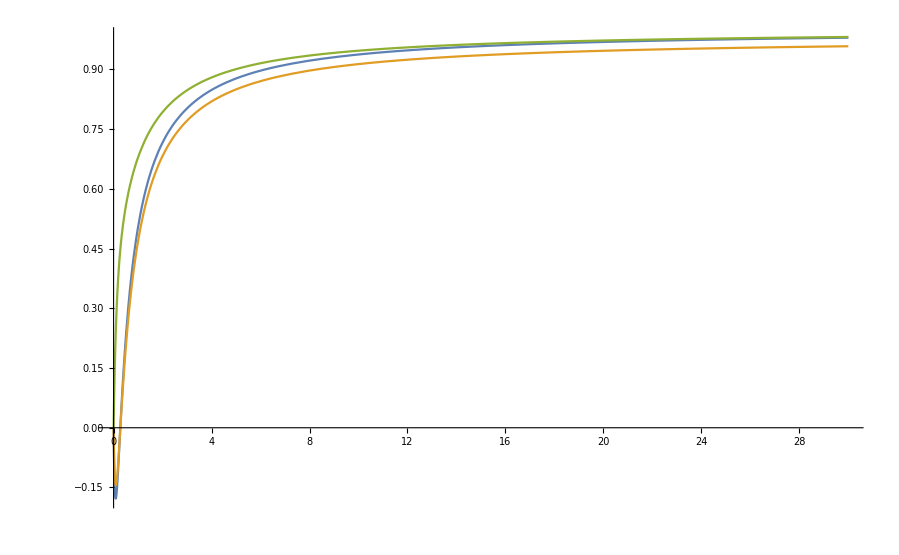

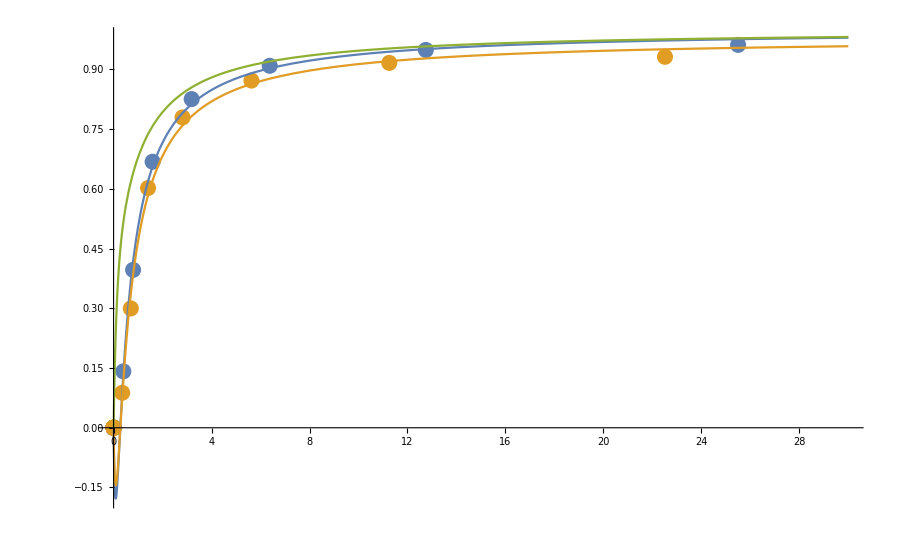

```mathematica
(*transverse, measured at 256*64*256*)
L={1/2,1/4,1/8,1/16,1/32,1/64,1/128,0,0,0,0,0,0,0}*8.284925963482451*10^-7;
a0=1.62462*10^-8;
mobwet0={0.9618,0.9491,0.9093,0.8256,0.6683,0.3966,0.1416,0,0,0,0,0,0,0};
ratio0=L/a0;
curve0=Thread[{ratio0,mobwet0}]

a1=1.84*10^-8;
mobwet1={0.9318,0.9166,0.8721,0.7795,0.6022,0.2997,0.08781,0,0,0,0,0,0,0};
ratio1=L/a1;
curve1=Thread[{ratio1,mobwet1}]

fitfunc2=aa+bb 1/(x+ctf)+cc 1/(x+ctf)^3;
fit0[x_]=fitfunc2/. FindFit[ curve0,fitfunc2,{aa,bb,cc,ctf},x]
fit1[x_]=fitfunc2/. FindFit[ curve1,fitfunc2,{aa,bb,cc,ctf},x]

p1=ListPlot[{curve0,curve1},PlotRange->All];
p2=Plot[{fit0[x],fit1[x],infplaneT[x a0,a0]},{x,0,30},PlotRange->All]
Show[p1,p2,PlotRange->All]
```

{{25.498,0.9618},{12.749,0.9491},{6.37451,0.9093},{3.18726,0.8256},{1.59363,0.6683},{0.796814,0.3966},{0.398407,0.1416}}

{{22.5134,0.9318},{11.2567,0.9166},{5.62835,0.8721},{2.81417,0.7795},{1.40709,0.6022},{0.703543,0.2997},{0.351772,0.08781}}

0.977222-10.3514/(2.34431+x)^3-0.407416/(2.34431+x)

0.93777-17.5813/(2.72916+x)^3-0.198893/(2.72916+x)

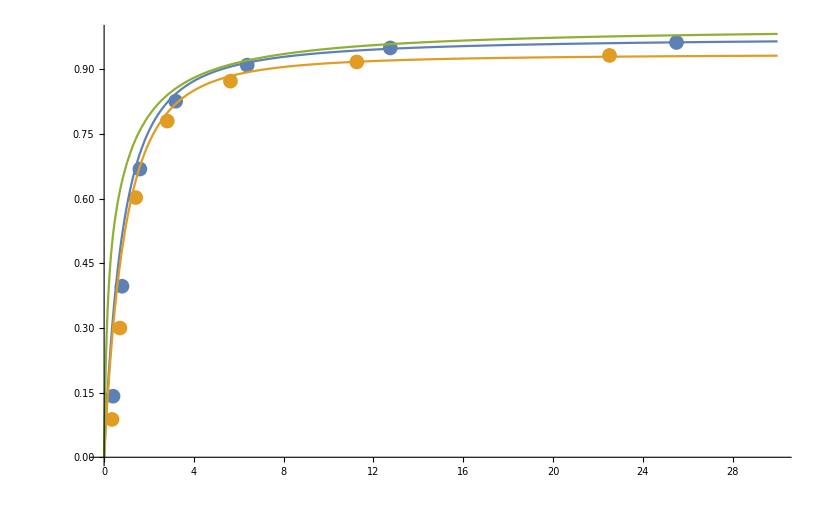

```mathematica
(*transverse, measured at 256*64*256*)
L={1/2,1/4,1/8,1/16,1/32,1/64,1/128}*8.284925963482451*10^-7;
a0=1.62462*10^-8;
mobwet0={0.9618,0.9491,0.9093,0.8256,0.6683,0.3966,0.1416};
ratio0=L/a0;
curve0=Thread[{ratio0,mobwet0}]

a1=1.84*10^-8;
mobwet1={0.9318,0.9166,0.8721,0.7795,0.6022,0.2997,0.08781};
ratio1=L/a1;
curve1=Thread[{ratio1,mobwet1}]

fitfunc2=aa+bb 1/(x+ctf)+cc 1/(x+ctf)^3;
fit0[x_]=0.9772218898770473-10.351356278332496/(2.3443146207089796+x)^3-0.40741625867115/(2.3443146207089796+x)
fit1[x_]=0.9377703455964084-17.581250246987494/(2.7291603741801147+x)^3-0.1988928626638771/(2.7291603741801147+x)

p1=ListPlot[{curve0,curve1},PlotRange->All];
p2=Plot[{fit0[x],fit1[x],infplaneT[x a0,a0]},{x,0,30},PlotRange->All];
Show[p1,p2,PlotRange->All]
```

```mathematica
Solve[MCSAN[0,a,LL]==0,cn]
```

$Aborted

```mathematica
fit0[x+0.2573093736888407]
```

0.977222-10.3514/(2.34431+x)^3-0.407416/(2.34431+x)

```mathematica
D[fit0[x],x]
```

31.0541/(2.34431+x)^4+0.407416/(2.34431+x)^2

```mathematica
MCSAN[0,a,LL]
```

Power::infy: Infinite expression 1/0 encountered.

0